# 相関円 （？）

```mathematica
cp[200]=CirclePoints[1,200];
```

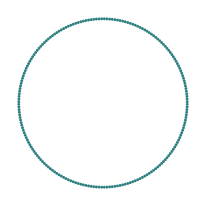

```mathematica
Graphics[{PointSize[0.01],RGBColor[0.18,0.5,0.5],pt=Map[Point,cp[200]]}]
```

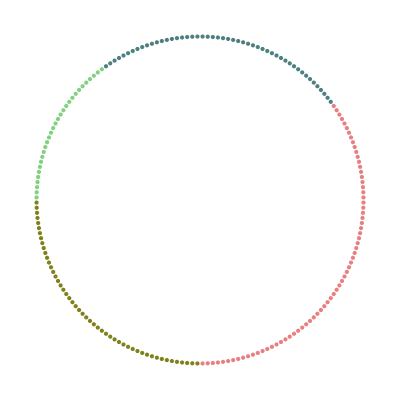

```mathematica
Graphics[ptGrp={RGBColor[0.91,0.5,0.5],pt[[1;;70]],RGBColor[0.3,0.5,0.5],pt[[71;;70+50]],RGBColor[0.5,0.82,0.5],pt[[70+50+1;;70+50+30]],RGBColor[0.5,0.5,0.11],pt[[70+50+30+1;;200]]}]
```

```mathematica
randomPair=Table[{RandomInteger[{1,200}],RandomInteger[{1,200}]},{70}];
```

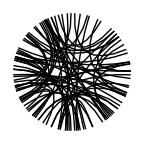

```mathematica
Graphics[bzpair=Map[BezierCurve[{cp[200][[#[[1]]]],{0,0},cp[200][[#[[2]]]]}]&,randomPair]]
```

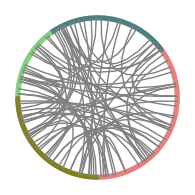

```mathematica
Graphics[{PointSize[0.02],ptGrp,RGBColor[0.5,0.5,0.5],bzpair}]
```

```mathematica
SplitBy[Range[20],Random[{0,10}]]
```

Random::randt: Random[{0,10}]でのタイプ指定{0,10}はReal，Integer，あるいはComplexでなければなりません．

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20}}